```mathematica
Clear[p,k];
Manipulate[Show[ContourPlot[-p^2+(-1/4+k/x)==0,{x,-10,10},{p,-10,10}],Graphics[Point[{4*k,0}]]],{{k,2},-2,2}]
Integrate[Sqrt[k/x-1/4],{x,0,4*k},Assumptions->x>0&&x<4*k]
```

k π

```mathematica
Clear[S,y]
Integrate[Sqrt[k/y-1/4],{y,0,x},Assumptions->y>0&&y<4*k&&x<4k&&x>0]
```

k π+1/2 √((4 k-x) x)-2 k ArcTan[√(-1+(4 k)/x)]

```mathematica
Clear[S,y,J]
S[x_,k_]:=k π+1/2 √((4 k-x) x)-2 k ArcTan[√(-1+(4 k)/x)];
J[x_,k_]:=2*Sqrt[k/x-1/4];
Limit[S[x,k],x->0]
```

0

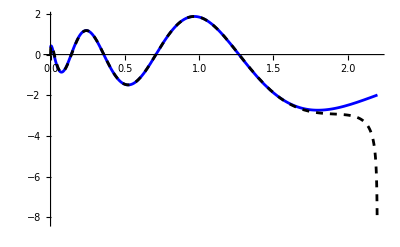

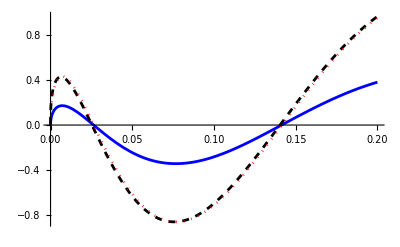

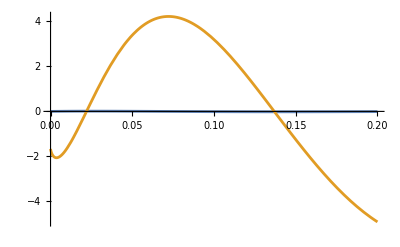

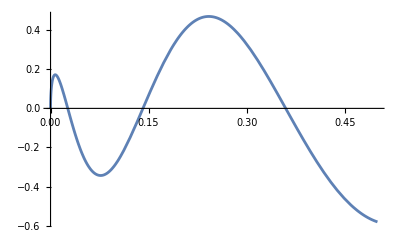

```mathematica
yas[x_,k_,h_]:=1/Sqrt[J[x,k]]*2*Cos[S[x,k]/h-Pi/4];
(*FullSimplify[DSolve[-h^2*y''[x]+(-1/4+k/x)*y[x]==0,y[x],x],Assumptions->h>0]*)
sol11:=NDSolve[{h^2*y''[x]+(-1/4+k/x)*y[x]==0,y[1]==yas[1,k,h],y'[1]==(D[yas[t,k,h],t])/.t->1},y[x],{x,-2,2}];
h:=0.1;
k:=h*(1/2+5);
Plot[{Evaluate[y[x]/.sol11],yas[x,k,h]},{x,0,4*k},PlotStyle->{Blue,{Black,Dashed}}]
Plot[{(*Evaluate[y[x]/.sol11]*)WhittakerM[k/h,0,x/h],yas[x,k,h],2*Sqrt[Pi*S[x,k]/h]/(2*Sqrt[Sqrt[k/x-1/4]])*BesselJ[0,S[x,k]/h]},{x,0,0.2},PlotStyle->{Blue,{Black,Dashed},{Red,Dotted}}]
Plot[{ⅇ^(-x/(2 h)) x (Hypergeometric1F1[1-11/2 √(1/h^2) h,2,√(1/h^2) x]),ⅇ^(-x/(2 h)) x ( HypergeometricU[-9/2,2,x/h])},{x,0,0.2}]
Plot[WhittakerM[k/h,0,x/h],{x,0,0.5}]
```

```mathematica
DSolve[h^2*y''[x]+(-1/4+k/x)*y[x]==0,y[x],x]
```

DSolve[(-1/4+0.55/x) y[x]+0.01 y''[x]==0,y[x],x]

```mathematica
BesselJ[0,0]
```

1

```mathematica
Limit[2*Sqrt[Pi*S[x,k]/h]/(2*Sqrt[Sqrt[k/x-1/4]]),x->0]
Limit[yas[x,k],x->0]
```

0.

0.

```mathematica
Clear[h];
FullSimplify[DSolve[h^2*y''[x]+(-1/4+k/x)*y[x]==0,y[x],x],Assumptions->h>0]
```

{{y[x]→(ⅇ^(-x/(2 h)) x (C[2] Hypergeometric1F1[1-11/2 √(1/h^2) h,2,√(1/h^2) x]+C[1] HypergeometricU[-9/2,2,x/h]))/(2 h^2)}}

```mathematica
Plot[]
```